```mathematica
Toy cycle:
R1, fixation: X1+A1 <--> 2 X2
R2, regeneration: X2+A2 <--> X1+A3
R3, transport:2X2 <--> 2 A4
```

```mathematica
ClearAll["Global`*"];
Clear[Derivative];
Remove["Global`*"];
Utilities`CleanSlate`
```

```mathematica
S={{-1,1,0},{2,-1,-1}};
MatrixForm[S]
```

(-1 | 1 | 0
2 | -1 | -1)

```mathematica
NullSpace[S]
```

{{1,1,1}}

```mathematica
Ex0={{ϵ11,ϵ12},{ϵ21,ϵ22},{0,ϵ32}};
Ex={{e11,e12},{e21,e22},{0,e32}};
MatrixForm[Ex0]
```

(ϵ11 | ϵ12
ϵ21 | ϵ22
0 | ϵ32)

```mathematica
CJmat0=Simplify[IdentityMatrix[3]-Ex0.Inverse[S.Ex0].S];
{C1,C2,C3}=CJmat0[[1]]
```

{(2 ϵ21 ϵ32)/(-ϵ12 ϵ21+ϵ11 (ϵ22-2 ϵ32)+2 ϵ21 ϵ32),(2 ϵ11 ϵ32)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32),(2 ϵ12 ϵ21-2 ϵ11 ϵ22)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32)}

```mathematica
{(-2 e21 e32)/(-2 e21 e32+2 e11 e32+e12 e21-e11 e22),(2 e11 e32)/(-2 e21 e32+2 e11 e32+e12 e21-e11 e22),(2 (e12 e21-e11 e22))/(-2 e21 e32+2 e11 e32+e12 e21-e11 e22)}
```

{-(2 e21 e32)/(e12 e21-e11 e22+2 e11 e32-2 e21 e32),(2 e11 e32)/(e12 e21-e11 e22+2 e11 e32-2 e21 e32),(2 (e12 e21-e11 e22))/(e12 e21-e11 e22+2 e11 e32-2 e21 e32)}

```mathematica
nCJmat0=Simplify[Inverse[DiagonalMatrix[{2j,2j,j}]].CJmat0.DiagonalMatrix[{2j,2j,j}]];
{nC1,nC2,nC3}=nCJmat0[[1]]
```

{(2 ϵ21 ϵ32)/(-ϵ12 ϵ21+ϵ11 (ϵ22-2 ϵ32)+2 ϵ21 ϵ32),(2 ϵ11 ϵ32)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32),(ϵ12 ϵ21-ϵ11 ϵ22)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32)}

```mathematica
{(-2 ϵ21 ϵ32)/(-2 ϵ21 ϵ32+2 ϵ11 ϵ32+ϵ12 ϵ21-ϵ11 ϵ22),(2 ϵ11 ϵ32)/(-2 ϵ21 ϵ32+2 ϵ11 ϵ32+ϵ12 ϵ21-ϵ11 ϵ22),(ϵ12 ϵ21-ϵ11 ϵ22)/(-2 ϵ21 ϵ32+2 ϵ11 ϵ32+ϵ12 ϵ21-ϵ11 ϵ22)}
```

{-(2 ϵ21 ϵ32)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32),(2 ϵ11 ϵ32)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32),(ϵ12 ϵ21-ϵ11 ϵ22)/(ϵ12 ϵ21-ϵ11 ϵ22+2 ϵ11 ϵ32-2 ϵ21 ϵ32)}

```mathematica
Simplify[nC1+nC2+nC3]
```

1

```mathematica
v1=k1*(A1*X1-X2^2/K1);
v2=k2*(A2*X2 - (A3*X1)/K2);
v3=k3*(X2^2 - A4^2/K3);
v={{v1},{v2},{v3}};
```

```mathematica
{X1p,X2p}={X1,X2}/.Simplify[Solve[S.v=={{0},{0}},{X1,X2}]][[2]];
J1=Simplify[v1/.{X1->X1p,X2->X2p}];
J2=Simplify[v2/.{X1->X1p,X2->X2p}];
J3=Simplify[v3/.{X1->X1p,X2->X2p}];
J={J1,J2,J3};
```

```mathematica
Table[N[J1/.{A1->Exp[2],A2->Exp[3],A3->Exp[1],A4->Exp[1],K1->1,K2->1,K3->1, k1->1, k2->1, k3->k}],{k,{1,2,5,10,100,1000,10000,100000}}]
```

{137.926,93.4707,59.225,47.9839,38.8588,38.0196,37.9364,37.9281}

```mathematica
e11=D[v1,X1];
e12=D[v1,X2];
e21=D[v2,X1];
e22=D[v2,X2];
e32=D[v3,X2];
```

```mathematica
CJmat=Simplify[IdentityMatrix[3]-Ex.Inverse[S.Ex].S];
{C1,C2,C3}=CJ=CJmat[[1]]
```

{(4 A3 K1 k2 k3 X2)/(2 A3 k2 (k1+2 K1 k3) X2+A1 k1 K1 K2 (-A2 k2+4 k3 X2)),(4 A1 k1 K1 K2 k3 X2)/(2 A3 k2 (k1+2 K1 k3) X2+A1 k1 K1 K2 (-A2 k2+4 k3 X2)),(2 k1 k2 (A1 A2 K1 K2-2 A3 X2))/(-2 A3 k2 (k1+2 K1 k3) X2+A1 k1 K1 K2 (A2 k2-4 k3 X2))}

```mathematica
Expand[Denominator[C1]]
```

-A1 A2 k1 K1 k2 K2+2 A3 k1 k2 X2+4 A3 K1 k2 k3 X2+4 A1 k1 K1 K2 k3 X2

```mathematica
nCJmat=Inverse[DiagonalMatrix[J]].CJmat.DiagonalMatrix[J];
{nC1,nC2,nC3}=nCJ=Simplify[nCJmat[[1]]];
```

```mathematica
nC3
```

(k1 k2 (A1 A2 K1 K2-2 A3 X2))/(-2 A3 k2 (k1+2 K1 k3) X2+A1 k1 K1 K2 (A2 k2-4 k3 X2))

```mathematica
Simplify[Denominator[C1]/.X2->X2p]
```

(√(K1 K3 (8 A4^2 (A3 k2+A1 k1 K2) k3 (2 A1 k1 K1 K2 k3+A3 k2 (k1+2 K1 k3))+A1^2 A2^2 k1^2 K1 k2^2 K2^2 K3)))/K3

```mathematica
p={k2->r2*k1,k3->r3*k1,A1->Exp[2],A2->Exp[3],A3->Exp[1],A4->Exp[1],K1->1,K2->1,K3->1};
```

```mathematica
{nC1sim,nC2sim,nC3sim}=FullSimplify[nCJ/.X2->X2p/.p,k1>0];
```

```mathematica
N[(nC1sim+nC2sim+nC3sim)/.{r2->2,r3->3}]
```

1.

```mathematica
plotnC1=Plot3D[nC1sim/.{r2->10^log10r2,r3->10^log10r3},{log10r2,-2,2},{log10r3,-2,2},PlotRange->{-0.1,1.6},PlotStyle->Blue,AxesLabel->{"Log10(k2/k1)","Log10(k3/k1)","nC1"}]
```

-Graphics3D-

```mathematica
plotnC2=Plot3D[nC2sim/.{r2->10^log10r2,r3->10^log10r3},{log10r2,-2,2},{log10r3,-2,2},PlotRange->{-0.1,1.6},PlotStyle->Green,AxesLabel->{"Log10(k2/k1)","Log10(k3/k1)","nC2"}]
```

-Graphics3D-

```mathematica
plotnC3=Plot3D[nC3sim/.{r2->10^log10r2,r3->10^log10r3},{log10r2,-2,2},{log10r3,-2,2},PlotRange->{-0.6,1.1},PlotStyle->Red,AxesLabel->{"Log10(k2/k1)","Log10(k3/k1)","nC3"}]
```

-Graphics3D-

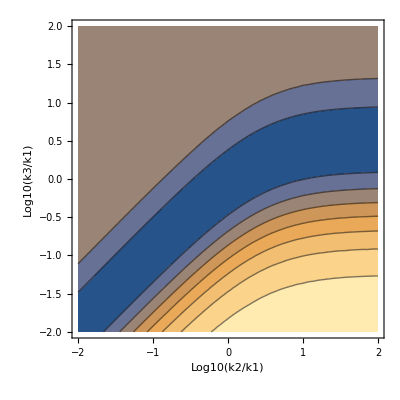

```mathematica
ContourPlot[nC3sim/.{r2->10^log10r2,r3->10^log10r3},{log10r2,-2,2},{log10r3,-2,2},PlotRange->{-0.6,1.1},PlotStyle->Red,AxesLabel->{"Log10(k2/k1)","Log10(k3/k1)"}]
```

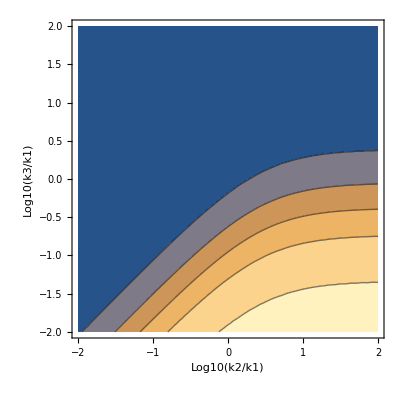

```mathematica
plotX2p=ContourPlot[FullSimplify[X2p/.p,k1>0]/.{r2->10^log10r2,r3->10^log10r3},{log10r2,-2,2},{log10r3,-2,2},PlotRange->Automatic,PlotStyle->Magenta,AxesLabel->{"Log10(k2/k1)","Log10(k3/k1)","X2"}]
```